# Pentakis Dodecahedron

### Author

Eric W. Weisstein
September 11, 2023

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polyhedra/PentakisDodecahedron.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/PentakisDodecahedron.html.

©2023 Wolfram Research, Inc. except for portions noted otherwise

## Solid

```mathematica
PolyhedronData["PentakisDodecahedron","Orientations"]
```

{C5}

```mathematica
Show[PolyhedronData[{"PentakisDodecahedron",#}],Boxed->False]&/@PolyhedronData["PentakisDodecahedron","Orientations"]
```

{-Graphics3D-}

### Solid and Dual

```mathematica
GraphicsRow[PolyhedronData["PentakisDodecahedron",#]&/@{"Graphics3D","Dual","DualCompound"}]
```

-Graphics-

### Net

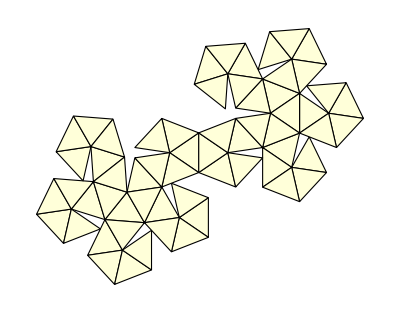

```mathematica
PolyhedronData["PentakisDodecahedron","Net"]
```

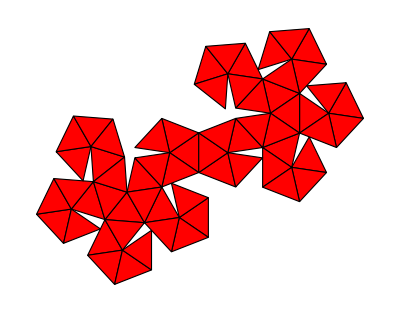

```mathematica
PolyhedronData["PentakisDodecahedron","Net","Colored"]
```

```mathematica
NetPrintout[PolyhedronData["PentakisDodecahedron","Polyhedron"],"PentakisDodecahedron.pdf"]
```

## Properties

#### Initialization

```mathematica
p=PolyhedronData[pname="PentakisDodecahedron","Polyhedron"]
```

Polyhedron[…]

```mathematica
vol=PolyhedronData[pname,"Volume"]
```

5/36 (41+25 √5)

### Centroid

```mathematica
PolyhedronData[pname,"Centroid"]
```

{0,0,0}

```mathematica
RegionCentroid[p]//FullSimplify//Timing
```

{5.49989,{0,0,0}}

```mathematica
(c=PolyhedronCentroid[p])//Timing
```

$Aborted

### Circumsphere

```mathematica
PolyhedronData[pname,"Circumsphere"]
```

Missing[NotApplicable]

```mathematica
Circumsphere[p]
```

Circumsphere::indep: Circumsphere does not exist for ….

Circumsphere[Polyhedron[…]]

```mathematica
MyCircumsphere[p]
```

{}

### ConvexHullOf

```mathematica
hullof=DeleteCases[Select[PolyhedronData[All],PolyhedronData[#,"ConvexHullName"]===pname&],pname]
```

{SmallTriambicIcosahedronHull}

```mathematica
GraphicsGrid[Partition[Graphics3D[{
{Green,Opacity[.8],PolyhedronData[#,"Polyhedron"]},
{Blue,Opacity[.2],PolyhedronData[#,"ConvexHull","Polyhedron"]}},Boxed->False,PlotLabel->Style[PolyhedronData[#,"Name"],Directive[14,Black,Italic,FontFamily->"Times"]]]&/@hullof,UpTo[3]],Dividers->All,ImageSize->200]
```

-Graphics-

### DihedralAngles

```mathematica
PolyhedronData[pname,"DihedralAngles"]//Tally
```

{{π-ArcCos[1/109 (80+9 √5)],90}}

```mathematica
DihedralAngles[p]//RootReduce//Tally
```

$Aborted

### EdgeLengths

```mathematica
PolyhedronData[pname,"EdgeLengths"]
```

{1,1/6 (9-√5)}

```mathematica
PolyhedronData[pname,"Lines"]/.Line[l_]:>EuclideanDistance@@l//FullSimplify//Union
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/12 (-11-3 √5)+1/12 (11+3 √5).

{1,1/6 (9-√5)}

### Faces

```mathematica
Show[GraphicsArray[partition[PolyhedronFaces[poly],15]]]
```

⁃GraphicsArray⁃

```mathematica
PolyhedronFaceCounts[poly]
```

{{60,3}}

### Insphere

```mathematica
PolyhedronData[pname,"Insphere"]
```

Sphere[{0,0,0},Root1.45Root[361-3816 #1^2+1744 #1^4&,4]1.4453319256522148]

```mathematica
Insphere[p]//RootReduce//Timing
```

$Aborted

```mathematica
MyInsphere[p]//RootReduce//Timing
```

$Aborted

### InertiaTensor

```mathematica
PolyhedronData[pname,"InertiaTensor"]
```

{{1/540 (263+93 √5),0,0},{0,1/540 (263+93 √5),0},{0,0,1/540 (263+93 √5)}}

```mathematica
MomentOfInertia[p]/Volume[p]//RootReduce//Timing
```

```mathematica
PolyhedronInertiaTensor[p]//RootReduce//Timing
```

$Aborted

### MeanCylindricalRadius

```mathematica
NIntegrate[√(x^2+y^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.869737

```mathematica
(i=Integrate[√(x^2+y^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"])//Timing
```

```mathematica
N[i]
```

### MeanCylindricalSquareRadius

```mathematica
NIntegrate[x^2+y^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]//FullSimplify
```

0.872138

```mathematica
(i=Integrate[x^2+y^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]//RootReduce)//Timing
```

{6.04681,1/540 (263+93 √5)}

```mathematica
N[i]
```

0.872138

### MeanSphericalRadius

```mathematica
NIntegrate[√(x^2+y^2+z^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.1073

```mathematica
(i=Integrate[√(x^2+y^2+z^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"])//Timing
```

```mathematica
N[i]
```

### MeanSphericalSquareRadius

```mathematica
NIntegrate[x^2+y^2+z^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

1.30821

```mathematica
(i=Integrate[x^2+y^2+z^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]//RootReduce)//Timing
```

{6.34517,1/360 (263+93 √5)}

```mathematica
N[i]
```

1.30821

### Midsphere

```mathematica
PolyhedronData[pname,"Midsphere"]
```

Sphere[{0,0,0},1/12 (11+3 √5)]

```mathematica
Midsphere[p]//RootReduce//Timing
```

$Aborted

### SurfaceArea

```mathematica
PolyhedronData[pname,"SurfaceArea"]
```

5/3 √(1/2 (421+63 √5))

```mathematica
RootReduce[%]
```

Root27.9Root[24593125-94725 #1^2+81 #1^4&,4]27.935249600700793

```mathematica
SurfaceArea[p]//RootReduce//Timing
```

{7.92622,Root27.9Root[24593125-94725 #1^2+81 #1^4&,4]27.935249600700793}

```mathematica
Total[Area/@PolyhedronData[pname,"Polygons"]]//RootReduce//Timing
```

{6.91457,Root27.9Root[24593125-94725 #1^2+81 #1^4&,4]27.935249600700793}

### VertexSubsetHulls

```mathematica
(h=VertexSubsetHulls[p,"Platonic"])//Timing
```

Finding equilateral triangles...

Finding potential tetrahedra from equilateral triangles...

Finding tetrahedra from potential candidates...

Finding cubes from tetrahedra...

Finding dodecahedron from cubes...

Finding octahedra by building up from equilateral triangles...

Finding dodecahedroa from octahedra...

Finding icosahdra by building up from equilateral triangles...

{4.16983,{Tetrahedron→{{1,16,20,24},{1,17,18,25},{9,14,20,27},{9,17,21,23},{10,15,18,26},{10,16,19,23},{11,13,19,27},{11,15,22,24},{12,13,21,26},{12,14,22,25}},Cube→{{1,12,13,16,20,21,24,26},{1,11,13,17,18,19,25,27},{9,10,14,15,18,20,26,27},{9,11,15,17,21,22,23,24},{10,12,14,16,19,22,23,25}},Icosahedron→{{2,3,4,5,6,7,8,28,29,30,31,32}},Dodecahedron→{{1,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27}}}}

```mathematica
g=Function[poly,Graphics3D[{
{Gray,Opacity[.2],EdgeForm[Thick],PolyhedronData[p,"Faces"]},ConvexHull3D[N[PolyhedronData[p,"VertexCoordinates"]][[#]]]&/@poly},Boxed->False]]/@h[[All,2]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Volume

```mathematica
PolyhedronData[pname,"Volume"]
```

5/36 (41+25 √5)

```mathematica
Volume[p]//FullSimplify
```

5/36 (41+25 √5)

```mathematica
PolyhedronVolume[p,Method->"GaussLaw"]//FullSimplify
```

5/36 (41+25 √5)

## Perspective projections

```mathematica
Manipulate[PolyhedronProjectionGraph[PolyhedronData["PentakisDodecahedron","Polyhedron"],{a,b,c}],{a,-1,1},{b,-1,1},{c,-1,1}]
```

### {-1/2,.11,1}

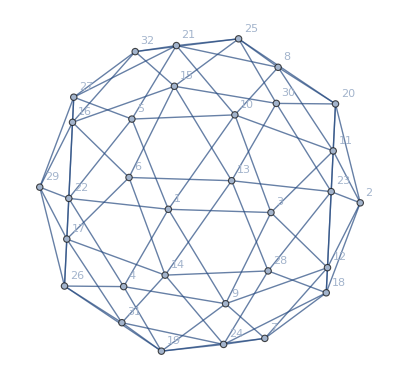

```mathematica
g=PolyhedronProjectionGraph[PolyhedronData["PentakisDodecahedron","Polyhedron"],{-1/2,.11,1},VertexLabels->"Name"]
```

### {-1/2,0,1}

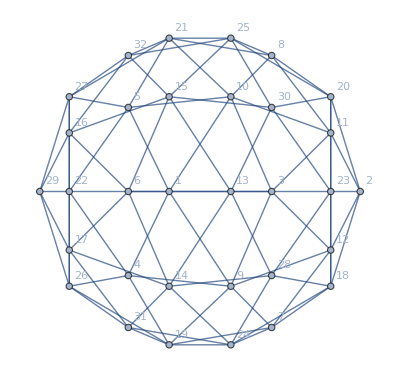

```mathematica
g=PolyhedronProjectionGraph[PolyhedronData["PentakisDodecahedron","Polyhedron"],{-1/2,0,1},VertexLabels->"Name"]
```

```mathematica
v=GraphEmbedding[g];
```

### {1,√(5-2 √5),-1/2 (-1+√5),-ArcCot[3 √(1+2/(√5))]}

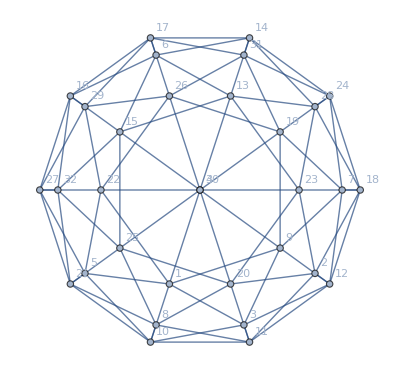

```mathematica
g=PolyhedronProjectionGraph[PolyhedronData["PentakisDodecahedron","Polyhedron"],{1,√(5-2 √5),-1/2 (-1+√5),-ArcCot[3 √(1+2/(√5))]},VertexLabels->"Name"]
```

```mathematica
v=GraphEmbedding[g];
```

```mathematica
ArcTan@@(v[[27]]-v[[18]])//FullSimplify
```

-π+ArcCot[3 √(1+2/(√5))]

```mathematica
g=PolyhedronProjectionGraph[PolyhedronData["PentakisDodecahedron","Polyhedron"],{1,y,-z},VertexLabels->"Name"]
```

```mathematica
v=GraphEmbedding[g];
```

```mathematica
FullSimplify[v[[4]]-v[[30]],y>0&&z>0]
```

{(5 (1+√5) y-√(250+110 √5) y^2+2 √(5 (5+2 √5)) z-√(250+110 √5) z^2)/(10 √((y^2+z^2) (1+y^2+z^2))),(-2 √(5 (5+2 √5)) y+5 (1+√5) z)/(10 √(y^2+z^2))}

```mathematica
Solve[Thread[Numerator[%]==0],{y,z}]//FullSimplify
```

{{y→0,z→0},{y→√(5-2 √5),z→1/2 (-1+√5)}}

```mathematica
N[%]
```

{{y→0.,z→0.},{y→0.726543,z→0.618034}}

### {1,√(5-2 √5),-1/11 (13-5 √5),ArcTan[√30]}

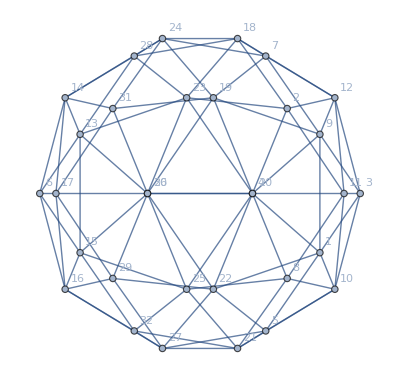

```mathematica
g=PolyhedronProjectionGraph[PolyhedronData["PentakisDodecahedron","Polyhedron"],{1,√(5-2 √5),-1/11 (13-5 √5),ArcTan[√30]},VertexLabels->"Name"]
```

```mathematica
v=GraphEmbedding[g];
```

```mathematica
ArcTan@@(v[[6]]-v[[3]])//FullSimplify
```

π-ArcTan[√30]

```mathematica
g=PolyhedronProjectionGraph[PolyhedronData["PentakisDodecahedron","Polyhedron"],{1,y,-z},VertexLabels->"Name"]
```

```mathematica
v=GraphEmbedding[g];
```

```mathematica
FullSimplify[v[[4]]-v[[20]],y>0&&z>0]
```

{((5+7 √5) y-√(410+178 √5) y^2+2 √(10-2 √5) z-√(410+178 √5) z^2)/(12 √((y^2+z^2) (1+y^2+z^2))),(-2 √(10-2 √5) y+(5+7 √5) z)/(12 √(y^2+z^2))}

```mathematica
Solve[Thread[Numerator[%]==0],{y,z}]//FullSimplify
```

{{y→0,z→0},{y→√(5-2 √5),z→1/11 (13-5 √5)}}

```mathematica
N[%]
```

{{y→0.,z→0.},{y→0.726543,z→0.165424}}

### {1,√(5-2 √5),-2+√5,-ArcTan[√15]}

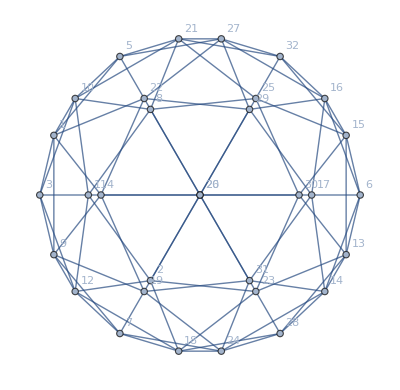

```mathematica
g=PolyhedronProjectionGraph[PolyhedronData["PentakisDodecahedron","Polyhedron"],{1,√(5-2 √5),-2+√5,-ArcTan[√15]},VertexLabels->"Name"]
```

```mathematica
v=GraphEmbedding[g];
```

```mathematica
ArcTan@@(v[[3]]-v[[6]])//FullSimplify
```

-π+ArcTan[√15]

```mathematica
g=PolyhedronProjectionGraph[PolyhedronData["PentakisDodecahedron","Polyhedron"],{1,y,z},VertexLabels->"Name"]
```

```mathematica
v=GraphEmbedding[g];
```

```mathematica
FullSimplify[v[[20]]-v[[26]],y>0&&z>0]
```

{(-5 (1+2 √5) y+√(725+310 √5) y^2-√(5 (65-22 √5)) z+√(725+310 √5) z^2)/(15 √((y^2+z^2) (1+y^2+z^2))),(-√(5 (65-22 √5)) y+5 (z+2 √5 z))/(15 √(y^2+z^2))}

```mathematica
Solve[Thread[Numerator[%]==0],{y,z}]//FullSimplify
```

{{y→0,z→0},{y→√(5-2 √5),z→-2+√5}}

```mathematica
N[%]
```

{{y→0.,z→0.},{y→0.726543,z→0.236068}}

### {0,1,0,-ArcTan[1/2 (-1+√5)]}

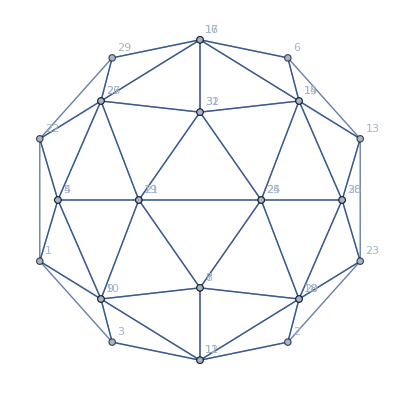

```mathematica
PolyhedronProjectionGraph[PolyhedronData["PentakisDodecahedron","Polyhedron"],{0,1,0,-ArcTan[1/2 (-1+√5)]},VertexLabels->"Name"]
```

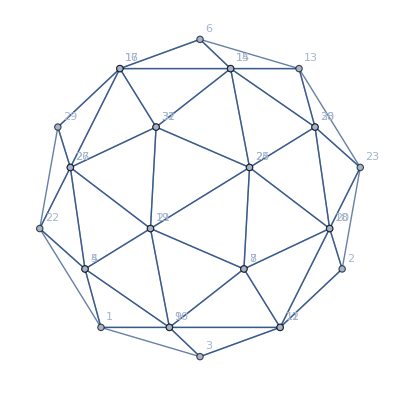

```mathematica
g=PolyhedronProjectionGraph[PolyhedronData["PentakisDodecahedron","Polyhedron"],{0,1,0},VertexLabels->"Name"]
```

```mathematica
v=GraphEmbedding[g];
```

```mathematica
ArcTan@@(v[[19]]-v[[24]])//FullSimplify
```

-π+ArcTan[1/2 (-1+√5)]

## Construction

```mathematica
PentakisDodecahedronExact=Dual[Polyhedron[TruncatedIcosahedron],Method->Semiregular];
```

```mathematica
Show[Graphics3D[PentakisDodecahedronExact],Boxed->False]
```

⁃Graphics3D⁃

## Net construction

```mathematica
PolyhedronData["PentakisDodecahedron","EdgeLengths"]
```

{1,1/6 (9-√5)}

```mathematica
({one,a}=SortBy[PolyhedronEdgeLengths[PolyhedronData["PentakisDodecahedron","Polyhedron"]]//RootReduce//Union,N]//Quiet)//Timing
```

{1.5892,{1,1/6 (9-√5)}}

```mathematica
{a}//N
```

{1.12732}

```mathematica
PolyhedronData["PentakisDodecahedron","FaceCountRules"]
```

{3→60}

```mathematica
Graphics3D[{poly=PolyhedronData["PentakisDodecahedron","Polyhedron"],MapIndexed[Text[#2[[1]],#,Background->White]&,v=PolyhedronData["PentakisDodecahedron","VertexCoordinates"]]}]
```

-Graphics3D-

```mathematica
Graphics3D[tri=Polygon[v[[{9,12,3}]]]]
```

-Graphics3D-

```mathematica
SortBy[ArcCos[ToAlgebraicRoot/@Cos[PolygonAngle[tri]]]//Quiet//FullSimplify,N]
```

{ArcCos[1/12 (9-√5)],ArcCos[1/12 (9-√5)],ArcCos[1/36 (-7+9 √5)]}

```mathematica
N[%]
```

{0.971985,0.971985,1.19762}

```mathematica
{α,β}=Union@%%
```

```mathematica
{α,β}={ArcCos[1/12 (9-√5)],ArcCos[1/36 (-7+9 √5)]};
```

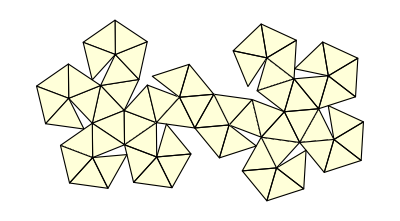

```mathematica
Rotate[PolyhedronData["PentakisDodecahedron","Net"],.55]
```

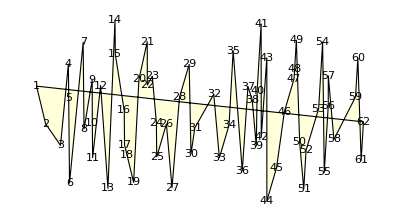

```mathematica
Graphics[{FaceForm[LightYellow,Red],EdgeForm[Black],Polygon[v=PolyhedronData["PentakisDodecahedron","NetCoordinates"],PolyhedronData["PentakisDodecahedron","NetFaceIndices"]],MapIndexed[Text[#2[[1]],#,Background->White]&,v]}]
```

```mathematica
EuclideanDistance@@@{v[[{31,28}]],v[[{32,28}]],v[[{31,32}]]}
```

{1.,1.,1.12732}

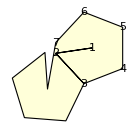

```mathematica
Graphics[{FaceForm[LightYellow,Red],EdgeForm[Black],Polygon[v,Take[f,5]],MapIndexed[Text[#2[[1]],#,Background->White]&,Take[v,7]]}]
```

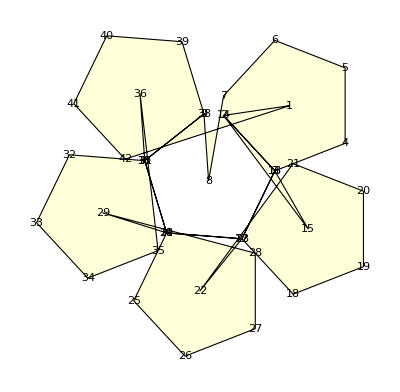

```mathematica
v=Join[{{0,0}},Table[Through[{Cos,Sin}[β/2+i β]],{i,-3,2}]]//N[#,10000]&;
v=Join[v,SimilarityTransform[v,{{7,6},{2,3}},Range[7]]];
v=Join[v,SimilarityTransform[v,{{3,2},{12,13}},Range[7]]];
v=Join[v,SimilarityTransform[v,{{3,2},{11,17}},Range[7]]];
v=Join[v,SimilarityTransform[v,{{3,2},{10,24}},Range[7]]];
v=Join[v,SimilarityTransform[v,{{3,2},{9,31}},Range[7]]];
f=Append[#,1]&/@Partition[Range[2,7],2,1];
f=Join@@Table[f+7i,{i,0,5}];
Graphics[{FaceForm[LightYellow,Red],EdgeForm[Black],Polygon[v,f],MapIndexed[Text[#2[[1]],#,Background->White]&,v]}]
```

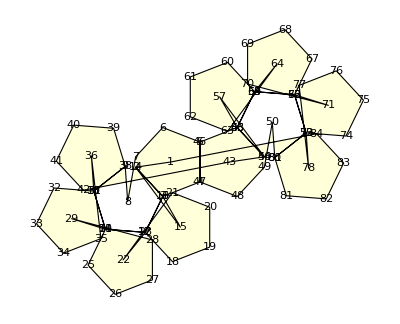

```mathematica
v=Join[v,SimilarityTransform[v,{{39,40},{5,4}},Range[42]]];
f=Join[f,f+42];
```

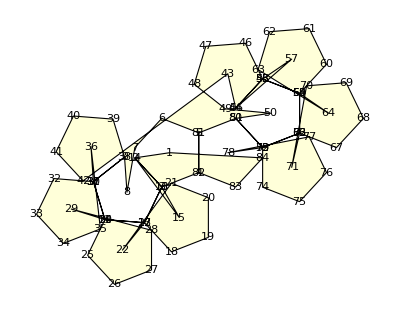

```mathematica
Graphics[{FaceForm[LightYellow,Red],EdgeForm[Black],Polygon[v,f],MapIndexed[Text[#2[[1]],#,Background->White]&,v]}]
```

```mathematica
60Area[Polygon[v,{{1,6,7}}]]//N
```

27.9352

```mathematica
PolyhedronData["PentakisDodecahedron","SurfaceArea"]//N
```

27.9352

```mathematica
Total[Area[Polygon[v,#]]&/@f]//N
```

27.9352

```mathematica
rot=RotationMatrix[{v[[46]]-v[[47]],{0,1}}]
```

{{0.,0},{0,0.}}

```mathematica
rot=IdentityMatrix[2];
```

```mathematica
v2=(rot.(#-v[[47]]))&/@v;
```

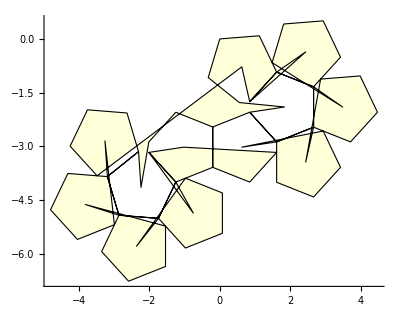

```mathematica
Graphics[{FaceForm[LightYellow,Red],EdgeForm[Black],Polygon[v2,f]},Axes->True]
```

```mathematica
vexact=Map[ToAlgebraicRoot[#,WorkingPrecision->1000]&,v2,{2}];//Timing
```

{41.1581,Null}

bug(426316): Area[Polygon[v, f]] returns wrong result

```mathematica
ToAlgebraicRoot@Area[Polygon[vexact,f]]//FullSimplify
```

-(√(5/2 (6970730047769+999640791387 √5)))/236196

```mathematica
ToAlgebraicRoot@Total[Area[Polygon[vexact,#]]&/@f]//FullSimplify
```

5/3 √(1/2 (421+63 √5))

```mathematica
PolyhedronData["PentakisDodecahedron","SurfaceArea"]
```

5/3 √(1/2 (421+63 √5))

```mathematica
vfinal=Union[vexact];
```

```mathematica
ffinal=Sort[vexact[[#]]&/@f/.Thread[vfinal->Range[Length[vfinal]]]]
```

{{1,48,47},{2,5,6},{2,39,27},{2,53,52},{4,55,13},{5,7,6},{7,9,6},{9,8,6},{10,22,12},{11,23,13},{14,15,40},{15,29,40},{16,17,41},{16,43,46},{17,16,46},{17,31,41},{18,19,21},{19,3,21},{20,18,21},{23,4,13},{24,10,12},{25,11,13},{25,26,21},{25,37,38},{26,20,21},{26,25,38},{26,35,12},{28,14,40},{30,16,41},{30,32,27},{30,39,40},{31,33,41},{32,30,41},{35,26,38},{35,36,12},{35,44,46},{36,24,12},{37,25,13},{37,42,47},{37,45,38},{39,2,6},{39,28,40},{39,30,27},{42,1,47},{43,34,46},{44,17,46},{44,35,38},{45,37,47},{48,62,47},{49,51,52},{50,49,52},{51,54,52},{53,2,27},{53,50,52},{53,61,57},{56,59,57},{58,56,57},{60,58,57},{61,53,27},{61,60,57}}

```mathematica
vfinal//FullSimplify
```

{{0,0},{-1/486 √(1/2 (2025641+828027 √5)),(-190107-88355 √5)/78732},{1/486 √(1/2 (2025641+828027 √5)),1/972 (-207-395 √5)},{1/486 √(1/2 (870221+306873 √5)),1/972 (765-161 √5)},{-(√(29135977+11068506 √5))/2187,-65/27-(31082 √5)/19683},{-(√(13403797+5993694 √5))/2187,-22/9-(29462 √5)/19683},{-(7 √(1/2 (2936129+1031571 √5)))/4374,-97/36-(143363 √5)/78732},{-(√(1/2 (47581409+19376397 √5)))/4374,-61/36-(124409 √5)/78732},{-(√(1/2 (47581409+19376397 √5)))/4374,-115/36-(111287 √5)/78732},{(2 √(707692378+193304718 √5))/19683,(-81243-26807 √5)/39366},{(2 √(707692378+193304718 √5))/19683,(-2511-7853 √5)/39366},{(28 √(1597813+602802 √5))/19683,(-82701-23567 √5)/39366},{(28 √(1597813+602802 √5))/19683,-(7 (567+659 √5))/39366},{(√(5 (20790257-9107154 √5)))/19683,(-92259-54311 √5)/39366},{(√(5 (20790257-9107154 √5)))/19683,(-16605-30436 √5)/19683},{-(√(1/2 (89788541-26346951 √5)))/19683,(-81243-26807 √5)/39366},{-(√(1/2 (89788541-26346951 √5)))/19683,(-11097-16684 √5)/19683},{(7 √(320707393+140494986 √5))/39366,-517/486-(8665 √5)/19683},{(√(1/2 (26563747709+10173135465 √5)))/39366,(-84321+1313 √5)/78732},{(√(1/2 (24426133121+8205807789 √5)))/39366,(-106353-53695 √5)/78732},{(√(9654110713+4129958178 √5))/39366,-(5 (8667+2818 √5))/39366},{(19 √(109/2 (340769+151875 √5)))/39366,-671/324-(17641 √5)/78732},{(19 √(109/2 (340769+151875 √5)))/39366,(-5589+20267 √5)/78732},{(√(1/2 (11052613541+4903275951 √5)))/39366,(-185085-72649 √5)/78732},{(√(1/2 (11052613541+4903275951 √5)))/39366,(-27621-34741 √5)/78732},{(√(1/2 (11052613541+4903275951 √5)))/39366,(-145719-21619 √5)/78732},{-(√(4255883533+1569406914 √5))/39366,(-60102-46085 √5)/39366},{-(√(3714277177-1001467638 √5))/39366,(-72576-70349 √5)/39366},{-(√(3714277177-1001467638 √5))/39366,(-52893-44834 √5)/39366},{-(√(3368703493-424781334 √5))/39366,-(95 (648+451 √5))/39366},{-(√(3368703493-424781334 √5))/39366,-517/486-(8665 √5)/19683},{-(√(1/2 (6344213141+2789224065 √5)))/39366,(-100521-66655 √5)/78732},{-(√(1/2 (6344213141+2789224065 √5)))/39366,(-106353-53695 √5)/78732},{(29 √(1/2 (6888389+1220913 √5)))/39366,(-100521-66655 √5)/78732},{(29 √(1/2 (6888389+1220913 √5)))/39366,(-106353-53695 √5)/78732},{(29 √(1/2 (6888389+1220913 √5)))/39366,(-224451-40573 √5)/78732},{(29 √(1/2 (6888389+1220913 √5)))/39366,(-66987-2665 √5)/78732},{(√(2646857737+1160738262 √5))/39366,-(5 (8667+2818 √5))/39366},{-(√(1/2 (4714128281+2093048181 √5)))/39366,-(89 (1377+1367 √5))/78732},{-(√(1/2 (2683183529-416426427 √5)))/39366,(-125469-115183 √5)/78732},{-(√(1/2 (2595254501+297385425 √5)))/39366,(-103437-60175 √5)/78732},{(√(1174353697+350203338 √5))/39366,-139/162+(8327 √5)/19683},{(√(5 (209494253+6483078 √5)))/39366,-(95 (648+451 √5))/39366},{(√(5 (209494253+6483078 √5)))/39366,-517/486-(8665 √5)/19683},{(√(5 (209494253+6483078 √5)))/39366,-(7 (6399+1550 √5))/39366},{(√(545/2 (1137181+489321 √5)))/39366,(-103437-60175 √5)/78732},{(√(545/2 (1137181+489321 √5)))/39366,(-69903+3815 √5)/78732},{-(4 √(744871618-238846554 √5))/177147,(-490383+48407 √5)/354294},{-(5 √(58352025433+25816978890 √5))/354294,(-666540-457997 √5)/354294},{-(√(5/2 (560047257769+167933475621 √5)))/354294,(-1338183-592237 √5)/708588},{-(√(1/2 (2663492452049+643880865789 √5)))/354294,(-1536471-1087309 √5)/708588},{-(7 √(20939732233+7345176210 √5))/354294,(-679662-428837 √5)/354294},{-(√(1/2 (1530716504249+459880204203 √5)))/354294,(-730197-892009 √5)/708588},{-(√(1/2 (1244230395221+449367909183 √5)))/354294,-(5 (378153+159725 √5))/708588},{(√(1/2 (534957397949+9115346601 √5)))/354294,(-423081-20555 √5)/708588},{-(√(23367250018753+10094378997618 √5))/1594323,(-827487-1765231 √5)/1594323},{-(√(13744047689485+5949974622870 √5))/1594323,(-886536-1634011 √5)/1594323},{-(7 √(1/2 (3142593297401+1217852174763 √5)))/3188646,-(19 (176625+218269 √5))/6377292},{-(95 √(1/2 (15581314529+5275729971 √5)))/3188646,(-5140467-8602759 √5)/6377292},{-(√(5/2 (14640595715461+6087664783665 √5)))/3188646,(2115999-6845059 √5)/6377292},{-(√(1/2 (55098493729049+23796375773877 √5)))/3188646,-(19 (353205+314407 √5))/6377292},{(√(5804080294177-1184899192758 √5))/3188646,(-4343886-591511 √5)/3188646}}

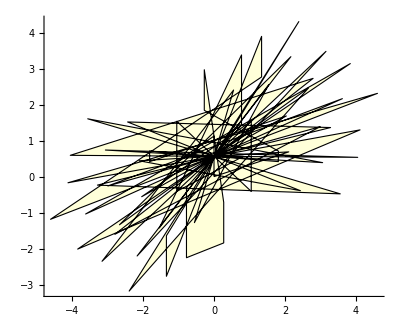

```mathematica
Graphics[{FaceForm[LightYellow,Red],EdgeForm[Black],Polygon[vfinal,ffinal]},Axes->True]
```

```mathematica
ToAlgebraicRoot@Total[Area[Polygon[vfinal,#]]&/@ffinal]//FullSimplify
```

5/3 √(1/2 (421+63 √5))